# POLINOMIOS DE HERMITE

Queremos Interpolar f(x_k)=P(x_k) y adicionalmente conservar la inclinación f'(x_k)=P'(x_k).

### TEOREMA

#### Si f∈C^1[a,b] y x_0,... ,x_n∈[a,b] son distintos, el único polinomio de menor grado que coincide con f y f’ en x_0,...,x_n es el polinomio de Hermite de grado a lo mas 2n+1, dado por:

#### PH_(2n+1)(x)=∑_(j=0)^n f(x_j)H_j(x)+∑_(j=0)^n f'(x_j)(Ĥ)_j(x)

#### donde

#### H_j(x) = (1 - 2 (x - x_j) L_j^1(x_j))L_j^2(x) (Ĥ)_j(x)=(x-x_j)L_j^2(x)

#### Además, si f∈C^(2n+2)[a,b], entonces:

#### f(x)=PH_(2n+1)(x)+((x-x_0)^2···(x-x_n)^2)/((2n+2)!)f^(2n+2)(ξ(x))

```mathematica
A={{"k","x_k","f(x_k)","f'(x_k)"},{0,1.3,0.6200860,-0.5220232},{1,1.6,0.4554022,-0.5698959},{2,1.9,0.2818186,-0.5811571}}//TableForm
```

k | x_k | f(x_k) | f'(x_k)
0 | 1.3 | 0.620086 | -0.522023
1 | 1.6 | 0.455402 | -0.569896
2 | 1.9 | 0.281819 | -0.581157

Esperamos que el polinomio de Hermite para estos datos sea de grado 5.

#### 1er Paso: Calcular polinomios de Lagrange

```mathematica
Subscript[L, 0][x_]:=((x-1.6)(x-1.9))/((1.3-1.6)(1.3-1.9))
```

```mathematica
Subscript[L, 1][x_]:=((x-1.3)(x-1.9))/((1.6-1.3)(1.6-1.9))
```

```mathematica
Subscript[L, 2][x_]:=((x-1.3)(x-1.6))/((1.9-1.3)(1.9-1.6))
```

#### 2do Paso: Calcular derivada de Lagrange en los puntos x_k

```mathematica
L0:=N[Subscript[L, 0]'[1.3]]
```

```mathematica
L1:=N[Subscript[L, 1]'[1.6]]
```

```mathematica
L2:=N[Subscript[L, 2]'[1.9]]
```

#### 3er Paso: Calcular los H_k(x)

```mathematica
Subscript[H, 0][x_]:=(1-2(x-1.3)L0)(Subscript[L, 0][x])^2
```

```mathematica
Subscript[H, 1][x_]:=(1-2(x-1.6)L1)(Subscript[L, 1][x])^2
```

```mathematica
Subscript[H, 2][x_]:=(1-2(x-1.9)L2)(Subscript[L, 2][x])^2
```

#### 4to Paso: Calcular los (Ĥ)_k(x)

```mathematica
Subscript[Ha, 0][x_]:=(x-1.3)(Subscript[L, 0][x])^2
```

```mathematica
Subscript[Ha, 1][x_]:=(x-1.6)(Subscript[L, 1][x])^2
```

```mathematica
Subscript[Ha, 2][x_]:=(x-1.9)(Subscript[L, 2][x])^2
```

#### 5to Paso: Felicidad

```mathematica
Subscript[PH, 5][x_]:=0.620086*Subscript[H, 0][x]+0.4554022*Subscript[H, 1][x]+0.2818186*Subscript[H, 2][x]-0.5220232*Subscript[Ha, 0][x]-0.5698959*Subscript[Ha, 1][x]-0.5811571*Subscript[Ha, 2][x]
```

```mathematica
Expand[Subscript[PH, 5][x]]
L[x_]:=0.620086*Subscript[L, 0][x]+0.4554022*Subscript[L, 1][x]+0.2818186*Subscript[L, 2][x]
```

1.00194-0.00822922 x-0.235216 x^2-0.0145561 x^3+0.0240318 x^4-0.00277469 x^5

```mathematica
Expand[L[x]]
```

1.23087-0.40556 x-0.0494433 x^2

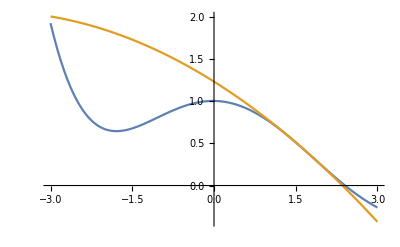

```mathematica
Plot[{Subscript[PH, 5][x],L[x]},{x,-3,3}]
```